```mathematica
getLogistic[h_,r_,x0_,y0_]:=Function[x,y0+(1/(1+Exp[-4/r(x-x0)])-0.5)2h]
```

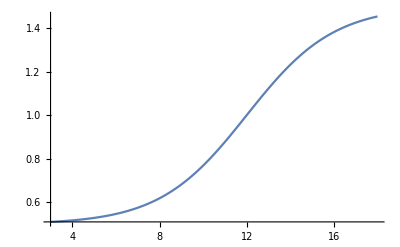

```mathematica
Plot[getLogistic[0.5,8,12,1][x],{x,3,18},PlotPoints->200]
```

```mathematica
getLogistic2[h1_,h2_,r_,x0_,y0_]:=(
hp=(h1+h2)/2;
yp=(y0+h1+y0-h2)/2;
xp=r/4 Log[(2hp)/(y0-yp+hp)-1]+x0;
getLogistic[hp,r,xp,yp]
)
```

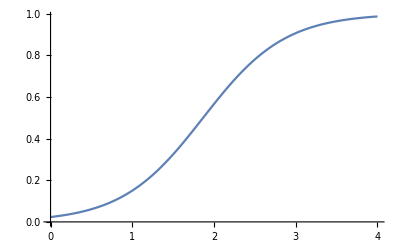

```mathematica
Plot[getLogistic2[0.85,0.15,2,1,0.15][x],{x,0,4},PlotPoints->200]
```